```mathematica
Exit[]
```

```mathematica
n=6;
```

```mathematica
BSE=-r V[t,S]+r S Derivative[0,1][V][t,S]+1/2 S^2 σ^2 Derivative[0,2][V][t,S]+Derivative[1,0][V][t,S]==0;
VS=Join[Table[Solve[D[BSE,{S,nn-2}],D[V[t,S],{S,nn}]][[1,1]],{nn,n,3,-1}],{Solve[D[BSE,t,{S,2}],D[V[t,S],{S,2},{t,2}]][[1,1]]}];
VS=#[[1]]->Simplify[#[[2]]/.VS]&/@VS;
VS=#[[1]]->Simplify[#[[2]]/.VS]&/@VS;
SN[x_]:= CDF[NormalDistribution[],x];
d[sk_,σ_,r_,T_]:=(Log[sk]+(r+σ^2/2)T)/σ/Sqrt[T];
BS[σ_,SK_,r_,T_]:=SK  SN[d[SK,σ,r,T]]-Exp[-r T]SN[d[SK,σ,r,T]-σ Sqrt[T]];
Moments=Table[W^nn->Limit[D[Exp[t^2/2],{t,nn}],t->0],{nn,2 n,1,-1}]
ExpValue[a_]:=Simplify[a-a+Expand[Normal[a ]]/.Moments]
Cov[a_,b_]:=Simplify[ExpValue[a b]-ExpValue[a]ExpValue[ b]]
Var[a_]:=Cov[a,a]
dX=μ dt^2+σ W dt;
dS=S (Series[Exp[dX],{dt,0,n}]-1);
dV=Series[V[t+dt^2,S+dS],{dt,0,n}]-V[t,S];
dP[Δ_]:=dV-Δ dS-(V [t,S]-Δ S)(Exp[dt^2 r]-1)
VarHedgingError[Δ_]:=Var[dP[Δ]]
```

{W^12→10395,W^11→0,W^10→945,W^9→0,W^8→105,W^7→0,W^6→15,W^5→0,W^4→3,W^3→0,W^2→1,W→0}

### Analysis

```mathematica
Cov[dS,dV]
```

S^2 σ^2 V^(0,1)[t,S] dt^2+1/2 S^2 σ^2 ((4 μ+3 σ^2) V^(0,1)[t,S]+2 S (μ+2 σ^2) V^(0,2)[t,S]+S^2 σ^2 V^(0,3)[t,S]+2 V^(1,1)[t,S]) dt^4+1/24 S^2 σ^2 (4 (12 μ^2+18 μ σ^2+7 σ^4) V^(0,1)[t,S]+3 S (20 μ^2+60 μ σ^2+41 σ^4) V^(0,2)[t,S]+12 S^2 μ^2 V^(0,3)[t,S]+96 S^2 μ σ^2 V^(0,3)[t,S]+121 S^2 σ^4 V^(0,3)[t,S]+12 S^3 μ σ^2 V^(0,4)[t,S]+36 S^3 σ^4 V^(0,4)[t,S]+3 S^4 σ^4 V^(0,5)[t,S]+48 μ V^(1,1)[t,S]+36 σ^2 V^(1,1)[t,S]+24 S μ V^(1,2)[t,S]+48 S σ^2 V^(1,2)[t,S]+12 S^2 σ^2 V^(1,3)[t,S]+12 V^(2,1)[t,S]) dt^6+O[dt]^8

```mathematica
Δ0=Simplify[Cov[dS,dV]/Var[dS]]
```

V^(0,1)[t,S]+(S (μ+2 σ^2) V^(0,2)[t,S]+1/2 S^2 σ^2 V^(0,3)[t,S]+V^(1,1)[t,S]) dt^2+1/24 (3 S (4 μ^2+16 μ σ^2+17 σ^4) V^(0,2)[t,S]+S^2 (12 μ^2+72 μ σ^2+103 σ^4) V^(0,3)[t,S]+3 (4 S^3 σ^2 (μ+3 σ^2) V^(0,4)[t,S]+S^4 σ^4 V^(0,5)[t,S]+4 (2 S (μ+2 σ^2) V^(1,2)[t,S]+S^2 σ^2 V^(1,3)[t,S]+V^(2,1)[t,S]))) dt^4+O[dt]^6

```mathematica
var10[S1_,σ1_,r1_,μ1_,t1_,t_]:=Normal[Simplify[VarHedgingError[Δ0]/.VS]/.V->(BS[σ,#2,r,1-#1]&)]/.σ->σ1/.r->r1/.t->t1/.μ->μ1/.dt->t/.S->S1
```

```mathematica
var8BS[S1_,σ1_,r1_,μ1_,t1_,t_]:=Normal[Simplify[VarHedgingError[Derivative[0,1][V][t,S]]/.VS]/.V->(BS[σ,#2,r,1-#1]&)]/.σ->σ1/.r->r1/.t->t1/.μ->μ1/.dt->t/.S->S1
```

```mathematica
σ1=0.2;μ1=.05;r1=-0.25;t1=0;S1=1;
```

```mathematica
v8BS=var8BS[S1,σ1,r1,μ1,t1,t]
```

0.00281611 t^4+0.000368441 t^6+0.000206457 t^8

```mathematica
v8=var8[S1,σ1,r1,μ1,t1,t]
```

0.00281611 t^4+0.000143152 t^6+0.000185994 t^8

```mathematica
v10=var10[S1,σ1,r1,μ1,t1,t]
```

0.00281611 t^4+0.000143152 t^6+0.000185994 t^8

0.0114254

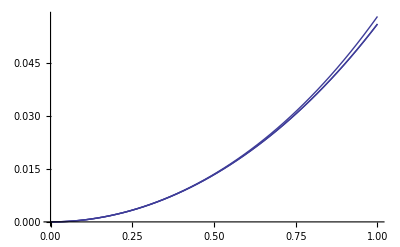

```mathematica
BS[σ,S,r,1-t]/.σ->σ1/.r->r1/.t->t1/.μ->μ1/.dt->t/.S->S1
Plot[Sqrt/@{v8,v8BS,v10},{t,0,Sqrt[1]}]
```

```mathematica
0.10450583572185568-Sqrt[v8/.t->1]
```

0.0484233

```mathematica
(*Test if equation is solved: *)
VarEq:=Simplify[D[#,t]+σ^2 S^2D[#,{S,2}]+μ S D[#,S]-2 r #+σ^2S^2(D[V[t,S],S]-Derivative[0,1][V][t,S])^2]&
Simplify[VarEq[VarHedgingError[Derivative[0,1][V][t,S]]]/.EW[4]->3];
```

```mathematica
var10[V_]:=1/2 S^4 σ^4 (Derivative[0,2][V][t,S])^2 dt^4-1/12 (S^2 σ^2 (S^2 (-32 r^2+σ^4+8 r (3 μ+σ^2)) (Derivative[0,2][V][t,S])^2+4 S (-10 r+6 μ+5 σ^2) Derivative[0,2][V][t,S] Derivative[1,1][V][t,S]-8 (Derivative[1,1][V][t,S])^2)) dt^6+1/12 S^2 (2 r S^2 (44 r^3+2 μ σ^4+σ^6-4 r^2 (16 μ+5 σ^2)+r (24 μ^2+16 μ σ^2+σ^4)) (Derivative[0,2][V][t,S])^2-S Derivative[0,2][V][t,S] ((-152 r^3+12 μ^2 σ^2+16 μ σ^4+5 σ^6+4 r^2 (52 μ+31 σ^2)-2 r (36 μ^2+56 μ σ^2+19 σ^4)) Derivative[1,1][V][t,S]+S σ^2 (36 r^2+12 μ^2+20 μ σ^2+9 σ^4-8 r (5 μ+4 σ^2)) Derivative[1,2][V][t,S])+2 ((32 r^2+12 μ^2+28 μ σ^2+15 σ^4-4 r (10 μ+9 σ^2)) (Derivative[1,1][V][t,S])^2+4 S σ^2 (-3 r+2 (μ+σ^2)) Derivative[1,1][V][t,S] Derivative[1,2][V][t,S]+S^2 σ^4 (Derivative[1,2][V][t,S])^2)) dt^8+1/(720 σ^2)S^2 (S^2 (7104 r^6-192 r^5 (95 μ+177 σ^2)+4 r σ^8 (197280 μ+965759 σ^2)+σ^10 (345600 μ+1843201 σ^2)+96 r^4 (160 μ^2+550 μ σ^2-137 σ^4)-96 r^3 (40 μ^3+40 μ^2 σ^2-2545 μ σ^4-6853 σ^6)-32 r^2 (15 μ^2 σ^4-20235 μ σ^6-83336 σ^8)) (Derivative[0,2][V][t,S])^2-4 (240 S^2 σ^2 (r^4+14 r^3 σ^2+71 r^2 σ^4+154 r σ^6+120 σ^8) Derivative[0,3][V][t,S] Derivative[1,1][V][t,S]-2 (888 r^4+180 μ^3 σ^2+540 μ^2 σ^4+525 μ σ^6-28633 σ^8-456 r^3 (5 μ+11 σ^2)+30 r^2 (52 μ^2+94 μ σ^2-527 σ^4)-6 r (60 μ^3+240 μ^2 σ^2+275 μ σ^4+6257 σ^6)) (Derivative[1,1][V][t,S])^2-6 S^2 σ^4 ((44 r^2-60 r μ+20 μ^2-76 r σ^2+60 μ σ^2+41 σ^4) (Derivative[1,2][V][t,S])^2+S σ^2 (-14 r+10 μ+13 σ^2) Derivative[1,2][V][t,S] Derivative[1,3][V][t,S]+S^2 σ^4 (Derivative[1,3][V][t,S])^2)+3 S σ^2 Derivative[1,1][V][t,S] ((552 r^3-120 μ^3-500 μ^2 σ^2-630 μ σ^4-253 σ^6-4 r^2 (250 μ+249 σ^2)+2 r (300 μ^2+700 μ σ^2+389 σ^4)) Derivative[1,2][V][t,S]+2 S σ^2 ((-48 r^2+60 r μ-20 μ^2+78 r σ^2-40 μ σ^2+9 σ^4) Derivative[1,3][V][t,S]+5 σ^2 (2 S (r+3 σ^2) Derivative[1,4][V][t,S]+S^2 σ^2 Derivative[1,5][V][t,S]+2 Derivative[2,3][V][t,S]))))+2 S Derivative[0,2][V][t,S] (120 S^2 σ^2 (-4 r^2+6 r μ+35 r σ^2+12 μ σ^2+82 σ^4) (r^3+12 r^2 σ^2+47 r σ^4+60 σ^6) Derivative[0,3][V][t,S]+120 S^3 σ^4 (r^4+18 r^3 σ^2+119 r^2 σ^4+342 r σ^6+360 σ^8) Derivative[0,4][V][t,S]+7104 r^5 Derivative[1,1][V][t,S]-18240 r^4 μ Derivative[1,1][V][t,S]+13920 r^3 μ^2 Derivative[1,1][V][t,S]-3360 r^2 μ^3 Derivative[1,1][V][t,S]-37056 r^4 σ^2 Derivative[1,1][V][t,S]+36960 r^3 μ σ^2 Derivative[1,1][V][t,S]-8400 r^2 μ^2 σ^2 Derivative[1,1][V][t,S]+960 r μ^3 σ^2 Derivative[1,1][V][t,S]-75624 r^3 σ^4 Derivative[1,1][V][t,S]+96000 r^2 μ σ^4 Derivative[1,1][V][t,S]+1920 r μ^2 σ^4 Derivative[1,1][V][t,S]-120 μ^3 σ^4 Derivative[1,1][V][t,S]+77532 r^2 σ^6 Derivative[1,1][V][t,S]+222960 r μ σ^6 Derivative[1,1][V][t,S]-240 μ^2 σ^6 Derivative[1,1][V][t,S]+665020 r σ^8 Derivative[1,1][V][t,S]+172650 μ σ^8 Derivative[1,1][V][t,S]+719974 σ^10 Derivative[1,1][V][t,S]-3312 r^4 S σ^2 Derivative[1,2][V][t,S]+6720 r^3 S μ σ^2 Derivative[1,2][V][t,S]-4320 r^2 S μ^2 σ^2 Derivative[1,2][V][t,S]+960 r S μ^3 σ^2 Derivative[1,2][V][t,S]+9480 r^3 S σ^4 Derivative[1,2][V][t,S]-7800 r^2 S μ σ^4 Derivative[1,2][V][t,S]+3480 r S μ^2 σ^4 Derivative[1,2][V][t,S]-360 S μ^3 σ^4 Derivative[1,2][V][t,S]+25140 r^2 S σ^6 Derivative[1,2][V][t,S]+3600 r S μ σ^6 Derivative[1,2][V][t,S]-840 S μ^2 σ^6 Derivative[1,2][V][t,S]+83130 r S σ^8 Derivative[1,2][V][t,S]-690 S μ σ^8 Derivative[1,2][V][t,S]+86142 S σ^10 Derivative[1,2][V][t,S]+696 r^3 S^2 σ^4 Derivative[1,3][V][t,S]-1080 r^2 S^2 μ σ^4 Derivative[1,3][V][t,S]+600 r S^2 μ^2 σ^4 Derivative[1,3][V][t,S]-120 S^2 μ^3 σ^4 Derivative[1,3][V][t,S]-1248 r^2 S^2 σ^6 Derivative[1,3][V][t,S]+1320 r S^2 μ σ^6 Derivative[1,3][V][t,S]-300 S^2 μ^2 σ^6 Derivative[1,3][V][t,S]+474 r S^2 σ^8 Derivative[1,3][V][t,S]+270 S^2 μ σ^8 Derivative[1,3][V][t,S]+963 S^2 σ^10 Derivative[1,3][V][t,S]-180 r^2 S^3 σ^6 Derivative[1,4][V][t,S]+180 r S^3 μ σ^6 Derivative[1,4][V][t,S]+540 S^3 μ σ^8 Derivative[1,4][V][t,S]+1500 S^3 σ^10 Derivative[1,4][V][t,S]-30 r S^4 σ^8 Derivative[1,5][V][t,S]+90 S^4 μ σ^8 Derivative[1,5][V][t,S]+435 S^4 σ^10 Derivative[1,5][V][t,S]+30 S^5 σ^10 Derivative[1,6][V][t,S]-120 r S^2 σ^6 Derivative[2,3][V][t,S]+180 S^2 μ σ^6 Derivative[2,3][V][t,S]+510 S^2 σ^8 Derivative[2,3][V][t,S]+90 S^3 σ^8 Derivative[2,4][V][t,S]+60 S σ^6 Derivative[3,2][V][t,S])) dt^10+O[dt]^11
```

```mathematica
1.1-55*(Exp[-0.25]-1)
```

13.266